```mathematica
II.1.e:
```

### (i):

```mathematica
ψ=1/(√2)({{1}, {0}, {0}, {1}});
ρ=ψ.Transpose[ψ];
ρ//MatrixForm
rA[i_]:=Tr[ρ.KroneckerProduct[IdentityMatrix[2],PauliMatrix[i]]];
rB[i_]:=Tr[ρ.KroneckerProduct[PauliMatrix[i],IdentityMatrix[2]]];
rAB[i_,j_]:=Tr[ρ.KroneckerProduct[PauliMatrix[i],PauliMatrix[j]]];
{rA[1],rA[2],rA[3]}
{rB[1],rB[2],rB[3]}
Table[rAB[i,j],{i,1,3},{j,1,3}]
```

(1/2 | 0 | 0 | 1/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/2 | 0 | 0 | 1/2)

{0,0,0}

{0,0,0}

{{1,0,0},{0,-1,0},{0,0,1}}

### (ii) :

```mathematica
ψ=1/(√2)({{0}, {1}, {-1}, {0}});
ρ=ψ.Transpose[ψ];
ρ//MatrixForm
rA[i_]:=Tr[ρ.KroneckerProduct[IdentityMatrix[2],PauliMatrix[i]]];
rB[i_]:=Tr[ρ.KroneckerProduct[PauliMatrix[i],IdentityMatrix[2]]];
rAB[i_,j_]:=Tr[ρ.KroneckerProduct[PauliMatrix[i],PauliMatrix[j]]];
{rA[1],rA[2],rA[3]}
{rB[1],rB[2],rB[3]}
Table[rAB[i,j],{i,1,3},{j,1,3}]
```

(0 | 0 | 0 | 0
0 | 1/2 | -1/2 | 0
0 | -1/2 | 1/2 | 0
0 | 0 | 0 | 0)

{0,0,0}

{0,0,0}

{{-1,0,0},{0,-1,0},{0,0,-1}}

## II.2:

```mathematica
ψ=1/(√2)({{0}, {1}, {-1}, {0}});
ρAB[x_]=x ψ.Transpose[ψ]+(1-x)/4 IdentityMatrix[4];
ρAB[x]//MatrixForm
```

((1-x)/4 | 0 | 0 | 0
0 | (1-x)/4+x/2 | -x/2 | 0
0 | -x/2 | (1-x)/4+x/2 | 0
0 | 0 | 0 | (1-x)/4)

### a)

```mathematica
Eigenvalues[ρAB[x]]
```

{(1-x)/4,(1-x)/4,(1-x)/4,1/4 (1+3 x)}

### b)

```mathematica
Solve[ρAB[x].ρAB[x]==ρAB[x],x]
```

{{x→1}}

### c)

```mathematica
Ry[ϕ_]=IdentityMatrix[2]Cos[ϕ/2]-I PauliMatrix[2]Sin[ϕ/2];
O1=Tr[ρAB[x].KroneckerProduct[PauliMatrix[1],Ry[ϕ].PauliMatrix[1].ConjugateTranspose[Ry[ϕ]]]]//FullSimplify
O2=Tr[ρAB[x].KroneckerProduct[PauliMatrix[3],Ry[ϕ].PauliMatrix[3].ConjugateTranspose[Ry[ϕ]]]]//FullSimplify
O3=Tr[ρAB[x].KroneckerProduct[PauliMatrix[1],Ry[ϕ].PauliMatrix[3].ConjugateTranspose[Ry[ϕ]]]]//FullSimplify
O4=Tr[ρAB[x].KroneckerProduct[PauliMatrix[3],Ry[ϕ].PauliMatrix[1].ConjugateTranspose[Ry[ϕ]]]]//FullSimplify
OAB=O1+O2+O3-O4
```

-x Cos[Re[ϕ]]

-x Cos[Re[ϕ]]

-x Sin[Re[ϕ]]

x Sin[Re[ϕ]]

-2 x Cos[Re[ϕ]]-2 x Sin[Re[ϕ]]

Los valores máximos se alcanzarán para x = 1 (el límite del máximo de x para que ρ represente un estado físico):

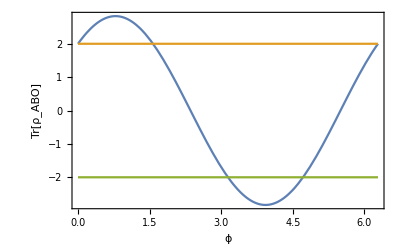

```mathematica
Plot[{2 √2 Cos[ϕ-π/4],2,-2},{ϕ,0,2 Pi},Frame->True,
FrameLabel->{"ϕ","Tr[ρ_ABO]"},
GridLines->{{Pi/4, 5 Pi/4},{}},
FrameStyle->Directive[Black,14]]
```

### d)

```mathematica
ρABtB=({{(1-x)/4, 0, 0, -x/2}, {0, (1-x)/4+x/2, 0, 0}, {0, 0, (1-x)/4+x/2, 0}, {-x/2, 0, 0, (1-x)/4}});
Eigenvalues[ρABtB]
```

{1/4 (1-3 x),(1+x)/4,(1+x)/4,(1+x)/4}

```mathematica
(*Es evidente que el único autovalor negativo va a ser el primero.*)
```

```mathematica
Negativity[x_]=-Min[0,Eigenvalues[ρABtB][[1]]]
```

-Min[0,1/4 (1-3 x)]

### e)

```mathematica
Rmat[x_]=FullSimplify[MatrixPower[MatrixPower[ρAB[x],1/2].KroneckerProduct[PauliMatrix[2],PauliMatrix[2]].Conjugate[ρAB[x]].KroneckerProduct[PauliMatrix[2],PauliMatrix[2]].MatrixPower[ρAB[x],1/2],1/2], Assumptions->{-1/3≤x≤1}];
Rmat[x]//MatrixForm
```

((1-x)/4 | 0 | 0 | 0
0 | (1+x)/4 | -x/2 | 0
0 | -x/2 | (1+x)/4 | 0
0 | 0 | 0 | (1-x)/4)

```mathematica
Eigenvalues[Rmat[x]]
```

{(1-x)/4,(1-x)/4,(1-x)/4,1/4 (1+3 x)}

```mathematica
Concurrence[x_]=FullSimplify[ Max[0,2Max[Eigenvalues[Rmat[x]]]-Tr[Rmat[x]]]]
FullSimplify[Concurrence[x],Assumptions->{0≤x≤1}]
```

Max[0,-1+2 Max[(1-x)/4,1/4 (1+3 x)]]

Max[0,-1/2+(3 x)/2]

```mathematica
-1+2 Max[(1-x)/4,1/4 (1+3 x)]
```

```mathematica
P[i_, x_]=(1+(-1)^i √(1-Concurrence[x]))/2
Eform[x_]=-Sum[P[i,x]Log2[P[i,x]],{i,0,1}];
```

1/2 (1+(-1)^i √(1+1/2 (1-3 x)))

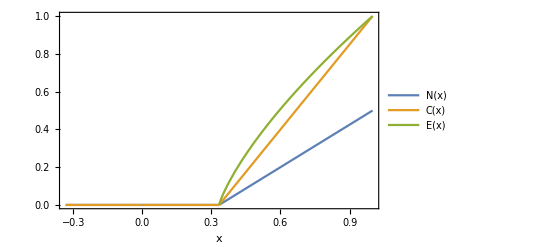

```mathematica
Plot[{Negativity[x],Concurrence[x],Eform[x]},{x,-1/3,1},Frame->True,FrameLabel->{"x",""},
FrameStyle->Directive[Black,14],PlotLegends->{"N(x)","C(x)","E(x)"},
GridLines->{{1/3},{}},
GridLinesStyle->Directive[Gray,Dashed]]
```